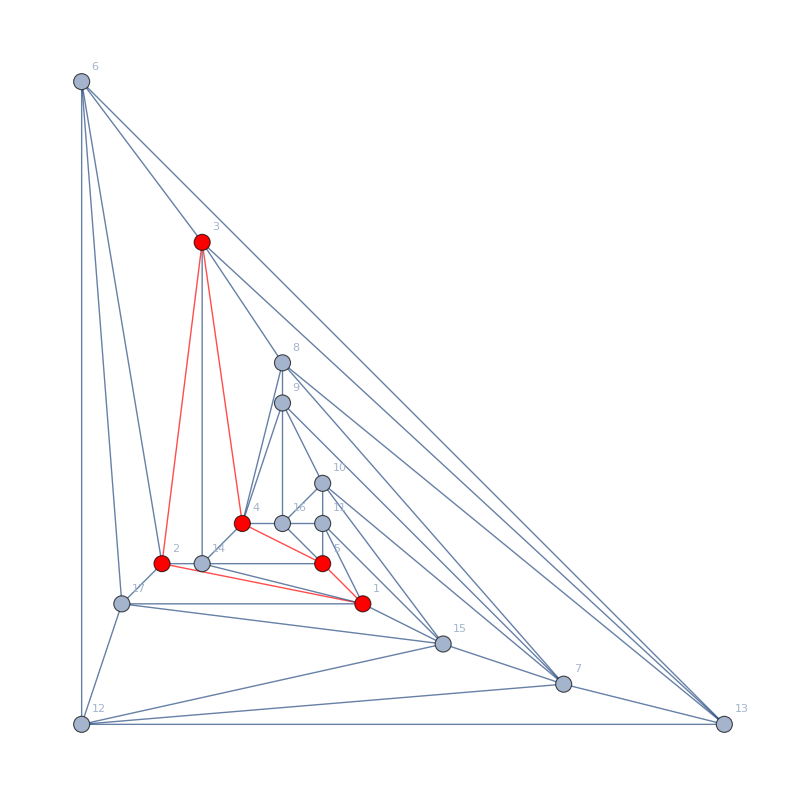

```mathematica
Graph[pl8,VertexStyle->{1 -> Red, 2 -> Red, 3 -> Red, 4 -> Red, 5 -> Red},EdgeStyle->{1<->2 -> Red, 2<->3 -> Red, 3<->4 -> Red, 4<->5 -> Red, 1<->5 -> Red},VertexSize->Large]
```

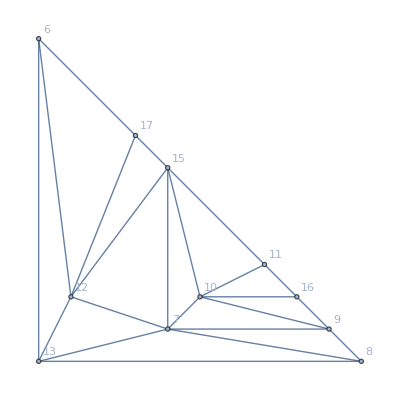

```mathematica
gxyz=VertexDelete[pl8,{1,2,3,4,5,14}]
```

```mathematica
VertexCount[gxyz]
```

11

```mathematica
gxyz2=pl8;
```

```mathematica
fxyz=FindFullFormula[gxyz]
```

{v6x7x8x9xaxbxcxdxfxgxh,v6x7x8x9bxaxcxdxfxgxh,v6x7x8gx9xaxbxcxdxfxh,v6x7x8gx9bxaxcxdxfxh,v6x7x8bx9xaxcxdxfxgxh,v6x7x8ax9xbxcxdxfxgxh,v6x7x8ax9bxcxdxfxgxh,v6gx7x8x9xaxbxcxdxfxh,v6gx7x8x9bxaxcxdxfxh,v6gx7x8bx9xaxcxdxfxh,v6gx7x8ax9xbxcxdxfxh,v6gx7x8ax9bxcxdxfxh,v6bx7x8x9xaxcxdxfxgxh,v6bx7x8gx9xaxcxdxfxh,v6bx7x8ax9xcxdxfxgxh,v6ax7x8x9xbxcxdxfxgxh,v6ax7x8x9bxcxdxfxgxh,v6ax7x8gx9xbxcxdxfxh,v6ax7x8gx9bxcxdxfxh,v6ax7x8bx9xcxdxfxgxh,12431,v69x7hx8cxaxbxdfg,v69x7hx8cgxaxbxdf,v69bx7hx8cxaxdfxg,v69bx7ghx8cxaxdf,v69bx7hx8cxaxdfg,v69bx7hx8cgxaxdf,v69x7bhx8cxaxdfxg,v69x7bhx8cxaxdfg,v69x7bhx8cgxaxdf,v69x7hx8bcxaxdfxg,v69x7ghx8bcxaxdf,v69x7hx8bcxaxdfg,v69x7hx8acxbxdfxg,v69x7ghx8acxbxdf,v69x7hx8acxbxdfg,v69bx7hx8acxdfxg,v69bx7ghx8acxdf,v69bx7hx8acxdfg,v69x7bhx8acxdfxg,v69x7bhx8acxdfg}
 |  |  |  |

```mathematica
(ChromaticPolynomial[gxyz2,4]/24)*120
```

2640

```mathematica
(ChromaticPolynomial[gxyz2,5]-2640)/120
```

36281

```mathematica
fxyz2=FindFullFormula[gxyz2];
```

$Aborted

```mathematica
star={1,2,3,4,5};
```

```mathematica
Map[With[
{rep=With[
{cols=With[{s=SymbolToSets[#]},Map[Select[#,!MemberQ[{7,10,12},#]&]&,s]]},
Table[
Table[k->Style[k,{Red,Blue,Yellow,Green}[[color]]],{k,cols[[color]]}],{color,Range[4]}
]
]},

Length[Select[rep,Length[#]≠0&]]->{6,17,15,11,16,9,8,13}/.Sort[Flatten[rep]]
]&,Select[fxyz2,SymbolLevel[#]==4&]]//Sort
```

```mathematica
Table[v->Sort[Select[Flatten[Map[{#[[1]],#[[2]]}&,IncidenceList[VertexDelete[pl8,14],v]]],!MemberQ[star,#]&]],{v,star}]
```

{1→{11,15,17},2→{6,17},3→{6,8,13},4→{8,9,16},5→{11,16}}

```mathematica
Map[With[
{rep=With[
{cols=With[{s=SymbolToSets[#]},Map[Select[#,!MemberQ[{7,10,12},#]&]&,s]]},
Table[
Table[k->Style[k,{Red,Blue,Yellow,Green}[[color]]],{k,cols[[color]]}],{color,Range[4]}
]
]},

Length[Select[rep,Length[#]≠0&]]->{6,17,15,11,16,9,8,13}/.Sort[Flatten[rep]]
]&,Select[fxyz,SymbolLevel[#]==4&]]//Sort
```

{2→{6,17,15,11,16,9,8,13},3→{6,17,15,11,16,9,8,13},3→{6,17,15,11,16,9,8,13},3→{6,17,15,11,16,9,8,13},3→{6,17,15,11,16,9,8,13},3→{6,17,15,11,16,9,8,13},3→{6,17,15,11,16,9,8,13},3→{6,17,15,11,16,9,8,13},3→{6,17,15,11,16,9,8,13},3→{6,17,15,11,16,9,8,13},3→{6,17,15,11,16,9,8,13},3→{6,17,15,11,16,9,8,13},3→{6,17,15,11,16,9,8,13},3→{6,17,15,11,16,9,8,13},3→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13},4→{6,17,15,11,16,9,8,13}}

```mathematica
Table[ChromaticPolynomial[gxyz,k],{k,1,15/2}]
```

{0,0,0,1608,162240,3997080,47328960}

```mathematica
67*120
```

8040

```mathematica
(162240-8040)/120
```

1285

```mathematica
1285*120
```

154200

```mathematica
Table[Length[Select[fxyz,SymbolLevel[#]==k&]],{k,1,15}]
```

{0,0,0,67,1285,4233,4504,1964,384,33,1,0,0,0,0}

```mathematica
Select[fxyz,SymbolLevel[#]==4&]
```

```mathematica
11103+1252+67
```

12422

```mathematica
Map[Sort[DeleteDuplicates[#]]&,Map[With[
{rep=With[
{cols=With[{s=SymbolToSets[#]},Map[Select[#,!MemberQ[{7,10,12},#]&]&,s]]},
Table[
Table[k->{Red,Blue,Yellow,Green}[[color]],{k,cols[[color]]}],{color,Range[4]}
]
]},

{6,17,15,11,16,9,8,13}/.Sort[Flatten[rep]]
]&,Select[fxyz,SymbolLevel[#]==4&]]]//Sort//Tally
```

{{{RGBColor[1, 0, 0],RGBColor[1, 1, 0]},1},{{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 1, 0]},12},{{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0]},2},{{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0]},52}}